```mathematica
u[x_, t_] := (t - .5x) / (1 + (t-.5x)^2)
```

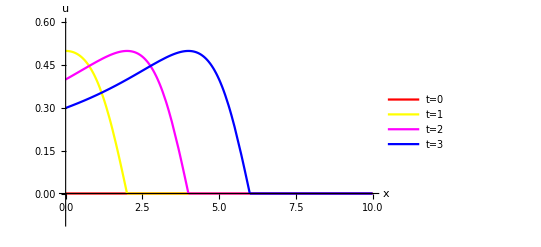

Null

```mathematica
p0 = Plot[Piecewise[{{u[x, 0], x< 2*(0)}, {0 , 2> x >(2*0)}}], {x, 0, 10}, PlotRange->{-.1, .6}, PlotStyle->Red, PlotLegends->{"t=0"}, AxesLabel->{Style["x",Bold,16],Style["u",Bold,16]}];
p1 = Plot[Piecewise[{{u[x, 1], x< 2*(1)}, {0 , 4 >x >2*(1)}}], {x, 0, 10}, PlotRange->{-.1, .6}, PlotStyle->Yellow, PlotLegends->{"t=1"}];
p2 = Plot[Piecewise[{{u[x, 2], x< 2*(2)}, {0 , 6 > x >(2*2)}}], {x, 0, 10}, PlotRange->{-.1, .6}, PlotStyle->Magenta, PlotLegends->{"t=2"}];
p3 = Plot[Piecewise[{{u[x, 3], x< 2*(3)}, {0 , x >2*(3)}}], {x, 0, 10}, PlotRange->{-.1, .6}, PlotStyle->Blue, PlotLegends->{"t=3"}];
Show[p0, p1, p2, p3]
```

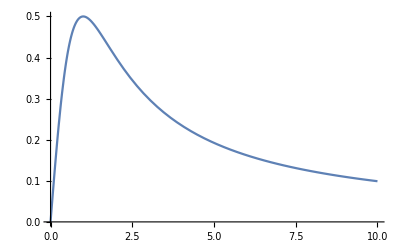

Null

```mathematica
Plot[u[0,t], {t, 0, 10}, PlotRange->Automatic]
```